# Sample Distribution

Normal Distribution

```mathematica
n=NormalDistribution[0.5,0.1]
```

NormalDistribution[0.5,0.1]

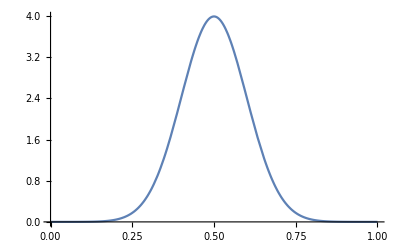

```mathematica
Plot[PDF[n,x],{x,0,1}]
```

```mathematica
n
```

NormalDistribution[0.5,0.1]

Population

```mathematica
Population=Table[RandomVariate[n],{i,1,1000}];
```

```mathematica
Mean[Population]
```

0.504084

```mathematica
Variance[Population]
```

0.0098354

Sample

```mathematica
Sample=Table[Mean[Table[RandomVariate[n],{i,1,1000}]],{i,1,100}];
```

```mathematica
Mean[Sample]
```

0.499899

```mathematica
Variance[Sample]
```

9.61351×10^-6

```mathematica
0.01/1000
```

0.00001

```mathematica
f[x_]:= Exp[0.4(x-0.4)^2-0.08 x^4]
```

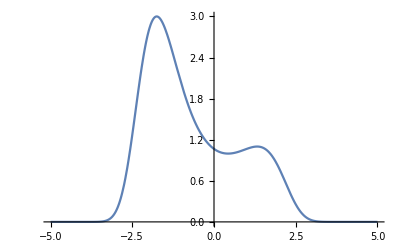

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
x:=10*RandomReal[]-5
```

```mathematica
y:=5*Random[]
```

```mathematica
sx=x;sy=y;
```

```mathematica
f[x]
```

0.998394

```mathematica
f[x]
```

0.00108828

```mathematica
Clear[L,Li,Outer]
```

Clear::wrsym: Symbol Outer is Protected.

```mathematica
Clear[sx,sy,L];
```

```mathematica
L={};LO={};
```

```mathematica
For[i=0,i<1000,i++,sx=x;sy=y;If[f[x]>y,L=Append[L,{sx,sy}],LO=Append[LO,{sx,sy}]]]
```

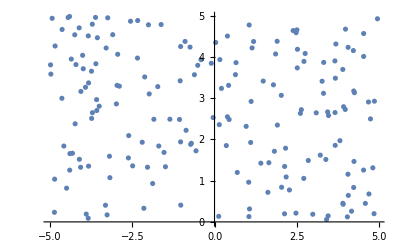

```mathematica
ListPlot[L]
```

```mathematica
ListPlot[{1,2},{2,3}]
```

ListPlot::nonopt: Options expected (instead of {2, 3}) beyond position 1 in ListPlot[{1, 2}, {2, 3}]. An option must be a rule or a list of rules.

ListPlot[{1,2},{2,3}]

```mathematica
sx
```

3.02002

```mathematica
sy=y;
```

```mathematica
sy
```

4.70979

```mathematica
If[f[x]>sy,f[x],0]
```

0

0.395422